```mathematica
c[x_]=200+25x+15/10 x^2
```

200+25 x+(3 x^2)/2

```mathematica
d[x_]=600-18 x
```

600-18 x

```mathematica
r[x_]=x d[x]//Expand
```

600 x-18 x^2

```mathematica
p[x_]=r[x]-c[x]//Expand
```

-200+575 x-(39 x^2)/2

```mathematica
N[brkev=Solve[p[x]==0,x]]
```

{{x→0.352029},{x→29.1352}}

```mathematica
N[d[x]/.brkev]
```

{593.663,75.5673}

```mathematica
N[xmax=First@Solve[p'[x]==0,x]]
```

{x→14.7436}

```mathematica
N[d[x]/.xmax]
```

334.615

```mathematica
N[p[x]/.xmax]
```

4038.78

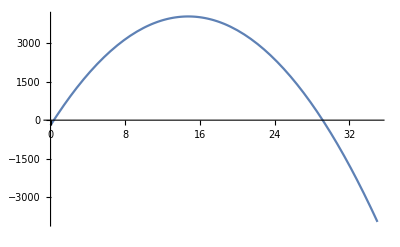

```mathematica
Plot[p[x],{x,0,35}]
```

```mathematica
cAvg[x_]=c[x]/x
```

(200+25 x+(3 x^2)/2)/x

```mathematica
cAvg'[x]//Simplify
```

3/2-200/x^2

```mathematica
Solve[cAvg'[x]==0,x]
```

{{x→-20/(√3)},{x→20/(√3)}}

```mathematica
xAcMin=First@NSolve[cAvg'[x]==0,x]
```

{x→11.547}

```mathematica
d[x]/.xAcMin
```

392.154